# CMSC389W Final Project: Types of continuity visualized and related theorems (math410)

## Sijing Yu 12/13/2019

## 1. Continuity in general In a general sense, a continuous function is a function which has no abrupt change, or “no break” in its graph. Technically, in Calculus I, we define that “A function f is continuous at a number a in its domain if lim_(x→a) f(x) = f(a) ” In this definition, three conditions are emphasized: a. f is defined at a, b. lim_(x→a) f(x) exists, c. lim_(x→a) f(x) equals f(a). Following are simple examples of functions discontinuous at x = 0 because of a. b. c. correspondingly.

```mathematica
p1=Plot[1/x,{x,-3,3}, PlotStyle->{Red,Thickness[.01]},PlotLabels->"1/x"]; p2=Plot[Abs[x]/x,{x,-3,3},PlotStyle->{Pink,Thickness[.01]}, PlotLabel->"|x|/x"]; p3=Plot[Piecewise[{{x^2,x<0},{x+1,x==0},{x^2,x>0}}],{x,-3,3},PlotStyle->{Orange,Thickness[.01]},PlotLabel->"x^2 with x = 1 at 0"];GraphicsRow[{p1,p2,p3},ImageSize->Full, Alignment->Center]
```

-Graphics-

## 2. Mathematical definition of continuity However, the definition above is not mathematically strong enough to verify the continuity of many complex functions, so we introduce δ - ϵ definition: “A function f : Domain(f) → ℝ is said to be continuous at a point a ∈ Domain(f) if for every ϵ > 0 there exists δ > 0 such that for every y ∈ Domain(f) we have | y - a | < δ ⟹ | f(y) - f(a) | < ϵ ” To explain in word, it means if we approach a point a arbitrarily close on the graph, this can be visualized below

```mathematica
functions={{If[x!=0,.1/x,x],If[x!=0,.1/x,x]},{If[x≥-.2,-(x+0.2)^(1/2)-.3,+(-x-0.2)^(1/2)-.3],(x+0.3)^3-.2},{2ArcSin[0.7 x]/Pi,Sin[Pi x/2.]/.7}};
Manipulate[With[{f=functions[[function,1]],g=functions[[function,2]]},Show[Plot[f,{x,-1,1},PlotRange->All,AspectRatio->Automatic,Ticks->None, ImageSize -> Large
],Graphics[{ Blue,PointSize[0.02],Point[{x0,f/.{x->x0}}],Line[{{x0,0},{x0,f/.{x->x0}}}],Line[{{0,f/.{x->x0}},{x0,f/.{x->x0}}}],Black,Dashed,
Line[{{x0-δ,0},{x0-δ,f/.{x->x0-δ}}}],Line[{{x0+δ,0},{x0+δ,f/.{x->x0+δ}}}],Line[{{0,f/.{x->x0-δ}},{x0-δ,f/.{x->x0-δ}}}],Line[{{0,f/.{x->x0+δ}},{x0+δ,f/.{x->x0+δ}}}],Orange,Line[{{0,(f/.{x->x0})+ϵ},{g/.{x->(f/.{x->x0})+ϵ},(f/.{x->x0})+ϵ}}],Line[{{0,(f/.{x->x0})-ϵ},{g/.{x->(f/.{x->x0})-ϵ},(f/.{x->x0})-ϵ}}],Thickness[0.01],Pink,Line[{{x0-δ,0},{x0+δ,0}}],Line[{{0,f/.{x->x0-δ}},{0,f/.{x->x0+δ}}}],PointSize[0.02],If[(f/.{x->x0+δ})>=(f/.{x->x0})+ϵ,{Orange,Point[{0,f/.{x->x0+δ}}]},{}],If[(f/.{x->x0-δ})<=(f/.{x->x0})-ϵ,{Orange,Point[{0,f/.{x->x0-δ}}]},{}],Black,Text[Style["x_0",10],{x0,-.05}],Text[Style["x_0-δ",10],{x0-δ,-.1}],Text[Style["x_0+δ",10],{x0+δ,-.1}],Text[Style["y_0-ϵ",10],{-.1,(f/.{x->x0})-ϵ}],Text[Style["y_0+ϵ",10],{-.1,(f/.{x->x0})+ϵ}],Text[Style["y_0",10],{-.1,(f/.{x->x0})}]}],PlotRange->{{-1,1},{-1,1}}]],{function,Range[3]},{{ϵ,0.1,"determine ϵ"},0.03,0.8},{{δ,0.1,"determine δ"},0.0001,0.8},
{{x0,0.5,"move x_0"},-1,1},SaveDefinitions->True,ControlPlacement->Left]
```

## 2. Uniform continuity From the graph above, for continuity at a point, we fix x first, then change δ and ϵ to verify continuity, we can see that the first function 1/x is not continuous at x = 0, because there is no δ that can make limit |1/x - ϵ| when x approaches x. This introduces us to uniform continuity, which describes continuity of a function in an interval instead of a point: “A function f : Domain(f) → ℝ is said to be uniformly continuous in if for every ϵ > 0, there exists δ > 0 such that for every x, y ∈ Domain(f) we have | y - x | < δ ⟹ | f(y) - f(x) | < ϵ Different from continuity, a is replaced with any point in the domain: x, which means for any two points on the graph, we can always limit their vertical distance to arbitrarily small number by limiting their horizontal distance, it’s like we can always find a rectangle with any fixed height -- 2ϵ and any width we want with a center on the graph -- ( x, f (x) ) such that the graph does not cut the height on its whole domain, which is shown below. Please make sure to download the gif file to your Mathematica directory and scroll the bar to see what I mean!

```mathematica
Import["uni_cts.gif","Animation",ImageSize -> Large]
```

## 3. Holder continuity By observing the graph we can easily understand what uniform continuity requires and how it is represented geometrically. Based on uniform continuity, we derive a more strict continuous condition -- Holder condition: “A function f : Domain(f) → ℝ is said to be Holder continuous if for every ϵ > 0, there exists a M > 0, α > 0 such that for every x, y ∈ Domain(f) we have | f(y) - f(x) | ≤ M|y-x|^α This is surely uniform continuous by letting δ equals ^α√ (ϵ/M), but it is more strict in the way that α implies the roughness of a path -- greater α implies less rough / nicer path. By roughness of a path, it can be shown here by Geometric Brownian Motions, blue -- roughest, yellow -- medium rough, green -- least rough.

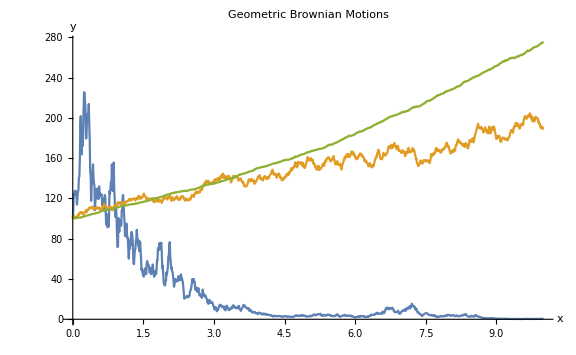

```mathematica
ListLinePlot[List[RandomFunction[GeometricBrownianMotionProcess[.1,1,100],{0,10,.01}],RandomFunction[GeometricBrownianMotionProcess[.1,0.1,100],{0,10,.01}],RandomFunction[GeometricBrownianMotionProcess[.1,0.01,100],{0,10,.01}]],AxesLabel->{"x","y"},PlotLabel->"Geometric Brownian Motions",ImageSize->Large]
```

## 4. Lipschitz continuity

## Starting from Holder continuous which allows α to give a greater range, we derive Lipschitz continuous with α = 1 in the Holder continuity: “A function f : Domain(f) → ℝ is said to be Lipschitz continuous if for every ϵ > 0, there exists a C > 0 such that for every x, y ∈ Domain(f) we have | f(y) - f(x) | ≤ C | y - x | This is strict in the way that the graph of the function must be outside a conic-section-shaped area formed by line of slope C and - C, as shown below

```mathematica
funcs[x_]:={Sin[x],Cos[x],x^2};
m={1,1,2 π};
Manipulate[DynamicModule[{plot=Dynamic[Plot[{funcs[a][[f]]+m[[f]](x-a),funcs[a][[f]]-m[[f]](x-a)},{x,-π,π},Filling->{1->{2}}, PlotStyle->{{Lighter[Purple,0.5],Thickness[0.005]}}][[1]]]},
Show[{Plot[funcs[x][[f]],{x,-π,π},PlotStyle->{Lighter[Pink,0.5],Thickness[0.005]}],Graphics[plot]},ImageSize->400,AspectRatio->1]],{{f,1,"function"},{1->ToString[Sin[x],TraditionalForm],2->ToString[Cos[x],TraditionalForm],3->ToString[x^2,TraditionalForm]},ControlType->Setter},{{a,-1,"a"},-π+.001, π-.001,Appearance->"Labeled"},SaveDefinitions->True]
```

## The graph above gives an idea of Lipschitz continuity, but we can not trust the graph for continuity since it x^2 seems to be Lipschitz continuous but it’s not by |f(n)−f(0)| / |n−0| = n^2/n = n at point n and 0, which reaches a contradiction.

## 4. Continuity and differentiability & integrability With understanding of continuity, we could understand differentiability better. By definition, “a function is differentiable at a point c if its derivative f(c)' =lim_(x→c) ( f(x) - f(c) ) / ( x - c )” exists at the point c.” Notice that the top limit of the top is what we decide continuity, but the bottom is out of continuity. The limit of the above fraction exists when its left and right limits are equal. Therefore, continuous functions are not necessarily differentiable: f (x) = |x| is a perfect example, with lim_(x→c+) ( f(x) - f(c) ) / ( x - c ) = 1, lim_(x→c-) ( f(x) - f(c) ) / ( x - c ) = -1 the limit does not exist at c = 0. It might seems obvious by considering |x| without absolute sign as a piecewise function, but here’s an another interesting example: ∑_(k=1)^∞ (αcos(k^β πx)+(1+α)sin(k^β πx))/k^β is continuous everywhere but not differentiable, as shown below.

```mathematica
Manipulate[Plot[Evaluate[Sum[((1-α) Sin[k^β Pi x]+α Cos[k^β Pi x])/k^β,{k,1,n}]],{x,0,1},PlotRange->{{0,1},{-1/2,3/2}},Filling->Axis,ImageSize->{500,325},MaxRecursion->ControlActive[1,6], PlotStyle->Pink, ImageSize->Full],{{n,24,"Number of terms"},1,100,1,Appearance -> "labeled"},Delimiter,{{β,3,"exponent β"},1,10,Appearance -> "labeled"},{{α,0,"cosine fraction α"},0,1,Appearance -> "labeled"},ControlPlacement->Left]
```

## Then we can see what differentiability means to function geometrically with sin[x] as a simple example.

```mathematica
f[x_] := x^3+x^2+x;
df[x_]:=3x^2+2x+1;
Manipulate[Show[Plot[ f[x],{x,x0-2 h,x0+2 h},PlotRange->{{x0-2*h,x0+2*h},{f[x0]-2*h,f[x0]+2*h}},Axes->If[hint,{True,True},{False,False}],
PlotStyle-> {Orange,Thickness[.005]},
Prolog->{GrayLevel[1],Disk[{x0,f[x0]},h],Pink,Circle[{x0,f[x0]},h]},
PlotLabel-> Row[{Style["f",Italic],"(",Style["x",Italic],")"}],Epilog-> {Pink,PointSize[.015], Point[{x0,f[x0]}]},AxesOrigin->{x0,f[x0]},Background-> GrayLevel[0.9],PlotStyle->Red,AspectRatio->1,ImagePadding->0.01],Graphics[{Line[{{x0-dx,df[x0](-dx)+f[x0]},{x0+dx,df[x0](dx)+f[x0]}}],{Red,Line[{{x0+dx,f[x0]},{x0+dx,df[x0](dx)+f[x0]}}],Line[{{x0,f[x0]},{x0+dx,f[x0]}}]}}],ImageSize -> Large],
{{x0,0.5,"x_0"},-1.46,0.5,Appearance->"Labeled"},
{{h,1,"zoom"},1,10^-6},
{{dx,0.3,"dx"},0.0001,0.301,0.001,Appearance->"Labeled"},
SaveDefinitions->True, ControlPlacement->Left]
```

## Although continuity does not necessarily imply differentiability, it does imply integrality in a closed, bounded interval. Continuous functions defined on closed, bounded interval have several nice properties: 1. They are bounded. 2. They actually achieve their bounds. 3. They are uniformly continuous. 4. They map convergent sequences to convergent sequences. (from StackExchange) Intuitively these conditions are good enough to make a continuous function integrable on a closed interval, as we can visualize below.

```mathematica
rectangles[f_,a_,b_,n_]:={Opacity[0.75],Red,N@Table[Rectangle[{a+k (b-a)/n,0},{a+(k+1) (b-a)/n,f[a+k (b-a)/n]}],{k,0,n-1}]}
(*This single function above is from https://reference.wolfram.com/language/ref/Integrate.html *)
          Linear[x_] := x+1; 
        Quad[x_]:=2 x^2+ Linear[x];
	Cubic[x_] := 3 x^3 + Quad[x];
	Exponential[x_] := Exp[x]
	Logarithm[x_] := Log[x] 
	SquareRoot[x_] := x^(1/2)
	Manipulate[Plot[ g[x],{x,0,20},Epilog -> rectangles[g,0,20,n],AxesOrigin-> {0,0}, PlotStyle->{Blue},AspectRatio->4/5, ImageSize -> {600,480}], {{g,Sin,"Custom"},{Sin ->Sin, Cos-> Cos,Linear-> "Linear" , Quad-> "Quadratic" , Cubic -> "Cubic", Exponential -> "Exponential", Logarithm -> "Logarithm", SquareRoot -> "SquareRoot"}},{{n,50,"number of rectangles"},0,100,1,Appearance->"Labeled"}]
```

## Conclusion: In general, we can get an order of continuity by strictness: Continuously differentiable ⊂ Lipschitz continuous ⊂ α-Hölder continuous ⊂ uniformly continuous = continuous with continuous function on closed&bounded interval → integrable, which gives us a better understanding of advanced calculus.

Sijing Yu - University of Maryland, College Park
MATH299M/CMSC389W Fall 2019
December 14th, 2019